```mathematica
SetDirectory["/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/t_all"]
fileList=FileNames["*.txt"];
Length[fileList]
tot=3.5*80-1
Monitor[data=Table[Import["/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/t_all/e_"<>IntegerString[i,10,3]<>"_i_"<>IntegerString[j,10,3]<>"_deltat_040.txt","Data"][[2;;All,1]],{i,0,tot},{j,0,tot}];,{i,j}]
Dimensions[data]
```

/home/ns-cclolab/Documents/ALEX_0605-20230605T073644Z-001/ALEX_0605/v1_logic_discrete/txnor

77603

279.

{280,280,490}

```mathematica
{If[data[[2,2,60]]>20,1,0],If[data[[2,2,140]]>20,1,0],If[data[[2,2,220]]>20,1,0]}
```

{0,0,0}

```mathematica
{1,1,1}
```

```mathematica
{1,1,1}
```

{1,1,1}

```mathematica
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[60]]>thresh,1,0],If[data[[140]]>thresh,1,0],If[data[[220]]>thresh,1,0],If[data[[490]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]

dat=Table[isGate[data[[i,j]],1],{i,1,tot+1},{j,1,tot+1}];
```

```mathematica
ListPlot[data[[20,20]]]
```

Part::partw: Part 20 of {«1»} does not exist.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

ListPlot[{{1},{1},{1},{1},{1},{1},{1},{1}}⟦20,20⟧]
 |  |  |  |

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

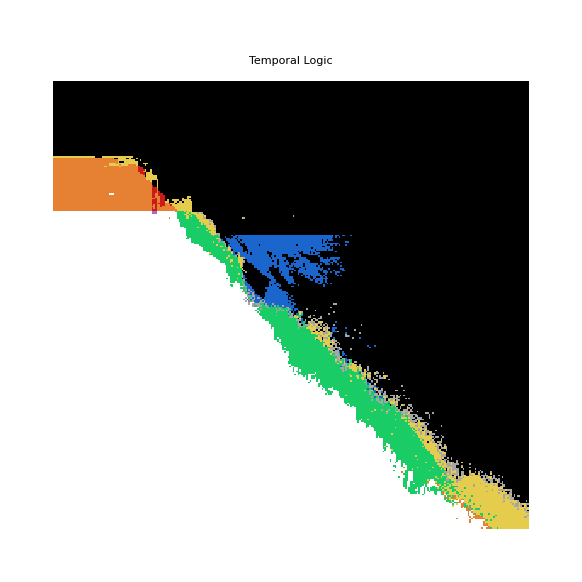

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[dat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{-1,3},{-1,3}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Temporal Logic","Title",Black,24]]
```

```mathematica
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.
```

```mathematica
0
```

```mathematica
data[[1,1,220]]
```

20.

```mathematica
0.0125^-1
```

80.

```mathematica
isGate[data[[1,1]],140]
```

8

```mathematica
dataq=data[[1,1]]
thresh=1
{If[dataq[[60]]>thresh,1,0],If[dataq[[140]]>thresh,1,0],If[dataq[[220]]>20,1,0],If[dataq[[450]]>thresh,1,0]}
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

1

{0,0,0,0}

```mathematica
{If[data[[1400]]>thresh,1,0],If[data[[140]]>thresh,1,0],If[data[[220]]>20,1,0],If[data[[450]]>thresh,1,0]}
```

Part::partw: Part 1400 of {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«440»} does not exist.

{If[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,20.,20.,20.,20.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,20.,20.,20.,20.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,20.,20.,20.,20.,20.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}⟦1400⟧>1,1,0],1,0,0}

{0.542419,0.504821,0.113192,0.721327,0.0353553,0.485251}

{0.113192,0.542419,0.504821,0.721327,0.485251,0.0353553}

8→Black,1→White,4→red,2→orange,3→yellow,5→green,7→blue,6→purple,

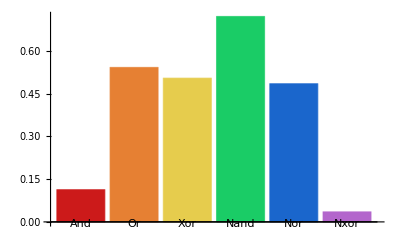

```mathematica
a=Sqrt[Table[Count[dat,i,Infinity],{i,2,7}]*.0125^2]
q=Permute[a,{2,3,1,4,6,5}]
"8→Black,1→White,4→red,2→orange,3→yellow,5→green,7→blue,6→purple,"
BarChart[q,ChartStyle->{red,orange,yellow,green,blue,purple},ChartLabels->{"And","Or","Xor","Nand","Nor","Nxor"},LabelStyle->{FontWeight->"Bold",FontSize->11}]
```